## Excision Radius Calculations

Investigating the excision radius function for the case of the BH.
The following parameters were considered: β=1, r_0=8 ,R_0=1.5, R_∞=1.9, Δ=0.05

```mathematica
β=1;r0=8;R0=1.5;Ri=1.9;Δ=0.05;
```

```mathematica
Recc[r_,c_]:=Ri(r/c)^β(1+(r/c)^(1/Δ))^(-β Δ)
Rcirc[r_]:=R0(r/r0)^β
```

Let’s root find a c for Recc that would set Recc=!=Rcirc when r=8M. In otherwords R_0=R_∞(r/c)^β(1+(r/c)^(1/Δ))^(-β Δ).

```mathematica
crule=NSolve[Recc[6,c]==R0,c,Reals][[1]]
Recc[9,c]/.crule
Recc2[r_]:=Recc[r,c]/.crule
```

{c→7.59662}

1.89685

Plotting out the two functions. Expectations: They must intersect at 8M (our “initial condition”).

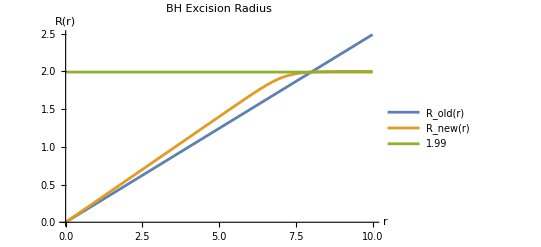

```mathematica
Plot[{Rcirc[r],Recc2[r],Recc[r,8],1.99},{r,0,10},AxesLabel->{"r","R(r)"},PlotLegends->{"R_old(r)","R_new(r)",1.99},PlotLabel->"BH Excision Radius"]
```

## KS ϕ Calculations

We wish to calculate circular angular velocity for Kerr in KS coordinate. We denote any quantity in KS coordinate with A_KS subscript. The only thing that between KS and Cart is the radial component; The azimuthal piece should be the same since it drops out always between y and z. In the equatorial we also expect θ to not factor in anymore.

```mathematica
Subscript[r, KS][a_,r_,z_]:=√(1/2(r^2-a^2+√((r^2-a^2)^2+4 a^2 z^2)))
FullSimplify[Subscript[r, KS][a,r,r Cos[θ]]/.θ->Pi/2,Assumptions->{r>a,r+a>0}]
%===FullSimplify[Subscript[r, KS][a,r,0],Assumptions->{r>a,r+a>0}]
FullSimplify[Subscript[r, KS][a,r,0],Assumptions->{r>a,r+a>0}]
```

√(-a^2+r^2)

True

√(-a^2+r^2)

Let’s do a test of solving for equatorial case and a=0.3 and r_KS=8, what the Cartesian radius is.

```mathematica
Subscript[r, KS][0.3,r,0]
NSolve[Subscript[r, KS][0.3,r,0]==8&&r>0,r]
```

(√(-0.09+r^2+√(0.+(-0.09+r^2)^2)))/(√2)

{{r→8.00562}}

We know that for Boyer-Lindquist coordinate: r^2=(r_BL^2+a^2)sin^2 θ+r_BL cos^2 θ. For equatorial orbits (θ=π/2), we get r_BL=√(r^2-a^2) .

```mathematica
BLtoCartrule=Subscript[r, BL]->√(r^2-a^2)
```

r_BL→√(-a^2+r^2)

Let’s generate the Cart->KS coord and from there we can obtain BL->KS coord transform rule within the confines of equatorial orbits.

```mathematica
CarttoKSrule=Solve[rks==Subscript[r, KS][a,r,0],r,PositiveReals]//FullSimplify
```

{{r→ConditionalExpression[√(a^2+rks^2), rks>0&&a>0]}}

```mathematica
BLtoKSrule={rbl->Subscript[r, BL]/.BLtoCartrule/.CarttoKSrule}[[1]]//FullSimplify//Normal
```

{rbl→rks}

We can now convert our azimuthal orbital velocity from BL->KS coordinates

```mathematica
ϕdot[a_,r_]:=1/(r^(3/2)+a) (*This is dϕ/dt in BL coords. Comes from eqn (2.16) of Bardeen (1972) et.al. Agrees to BHPertToolkit*)
ϕd=ϕdot[a,rbl]/.BLtoKSrule
ϕd/.{a->0.3,rks->8}
%==ϕdot[0.3,8]
v=ϕd rks/.{a->0.3,rks->8}(*Is this correct?*)
```

1/(a+rks^(3/2))

0.0436159

True

0.348927

The KS coordinates are defined according to https://spectre-code.org/classgr_1_1KerrSchildCoords.html as follows:

```mathematica
x=√(r^2+a^2)Sin[θ]Cos[φ+ArcTan[a/r]]
y=√(r^2+a^2)Sin[θ]Sin[φ+ArcTan[a/r]]
z=Cos[θ]
```